# GHZ STATES - IBMQ_16_melbourne

## N = 2

In this section the data refers to the measurement of qubit 0, with the parameter ϕ = (π j)/(n+1) that changes from 0 to (π (2n+1))/(n+1).

THEORY

```mathematica
n=2;
phi[j_]:=(Pi j)/(n+1)
S[ϕ_]:=1/2(1+Cos[n*ϕ])
Subscript[list, th]=Table[S[phi[j]],{j,0,(2*n+1)}];
```

```mathematica
Subscript[x, axis]=Table[phi[j],{j,0,(2*n+1)}];
```

```mathematica
Length[Subscript[x, axis]]==Length[Subscript[list, th]]
```

True

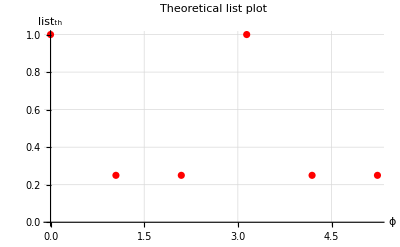

```mathematica
Subscript[listPlot, th]=ListPlot[Thread[{Subscript[x, axis],Subscript[list, th]}],AxesLabel->{HoldForm["ϕ"],HoldForm["list_th"]},PlotLabel->HoldForm["Theoretical list plot"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

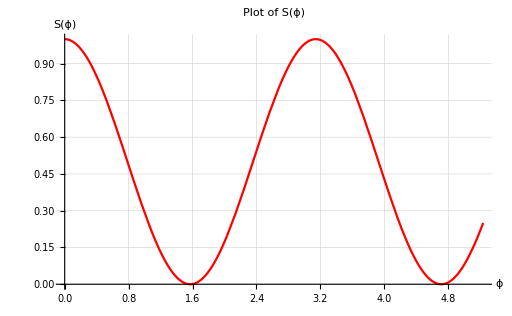

```mathematica
Subscript[plot, th]=Plot[S[ϕ],{ϕ,0,(Pi (2n+1))/(n+1)},AxesLabel->{HoldForm["ϕ"],HoldForm["S(ϕ)"]},PlotLabel->HoldForm["Plot of S(ϕ)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

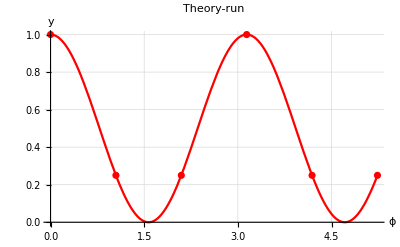

```mathematica
Show[Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, th]=Abs[N[Table[1/(2(n+1))*Sum[Exp[I  q phi[j]]*S[phi[j]],{j,0,(2*n+1)}],{q,-n,n}]]];
```

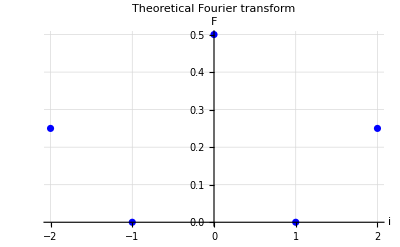

```mathematica
Subscript[FPlot, th]=ListPlot[Thread[{l,Subscript[F, th]}],AxesLabel->{HoldForm["i"],HoldForm["F"]},PlotLabel->HoldForm["Theoretical Fourier transform"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

SIMULATION

```mathematica
data1={1.0,0.2607421875,0.24609375,1.0,0.2529296875,0.2822265625};
```

#### Plot of the data choosen

```mathematica
simulation= data1
Length[simulation]
```

{1.,0.260742,0.246094,1.,0.25293,0.282227}

6

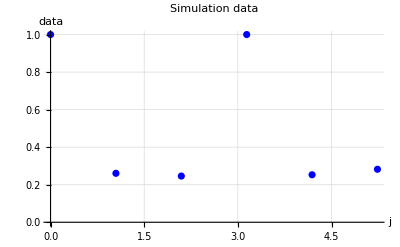

```mathematica
Subscript[plot, sim]=ListPlot[Thread[{Subscript[x, axis],simulation}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, sim]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*simulation[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

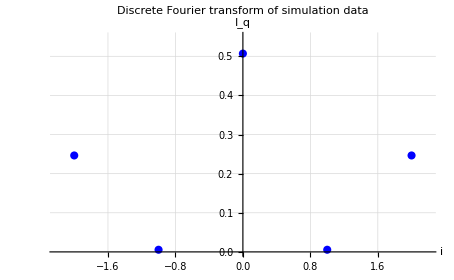

```mathematica
Subscript[I, sim]=Subscript[FPlot, sim]=ListPlot[Thread[{l,Subscript[F, sim]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{0,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

```mathematica
Lower=2 √(Subscript[F, sim][[Length[Subscript[F, sim]]]])
Upper=√(Subscript[F, sim][[n+1]]/2)+√(Subscript[F, sim][[Length[Subscript[F, sim]]]])
```

0.992995

0.999985

RUN

8192 shots

```mathematica
data1={0.892333984375,0.26318359375,0.3145751953125,0.90185546875,0.2664794921875,0.306884765625};
data2={0.9124755859375,0.2537841796875,0.3170166015625,0.9195556640625,0.255859375,0.313232421875};
data3={0.9451904296875,0.266357421875,0.32080078125,0.9447021484375,0.2642822265625,0.322998046875};
```

#### Plot of the data choosen

```mathematica
run=data2  (*inserire il data che si vuole*)
Length[run]
```

{0.912476,0.253784,0.317017,0.919556,0.255859,0.313232}

6

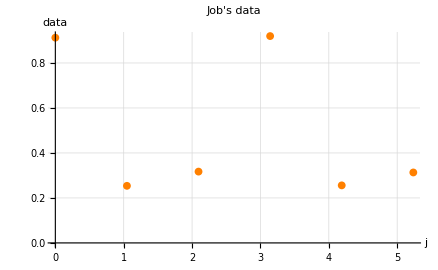

```mathematica
Subscript[plot, run]=ListPlot[Thread[{Subscript[x, axis],run}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Job's data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Orange}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, run]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*run[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

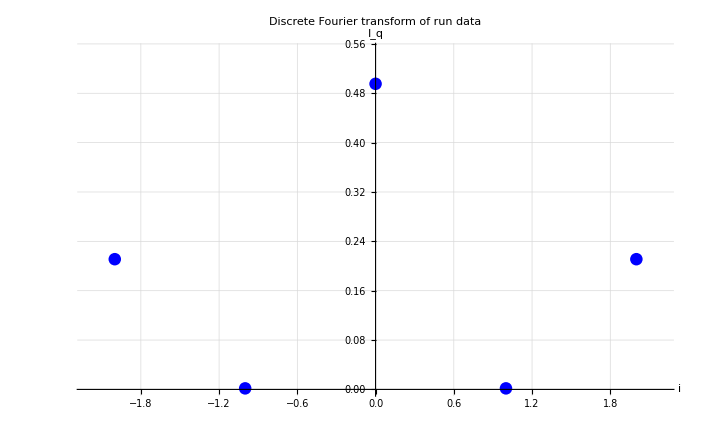

```mathematica
Subscript[I, run]=Subscript[FPlot, run]=ListPlot[Thread[{l,Subscript[F, run]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{0,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

Fidelity

```mathematica
F1=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data1[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}]
```

{0.203536,0.00258158,0.490885,0.00258158,0.203536}

```mathematica
F2=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data2[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

```mathematica
F3=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data3[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

```mathematica
F2Lower1= 2 √F1[[Length[F1]]]
F2Upper1=√(F1[[n+1]]/2)+√F1[[Length[F1]]]
```

0.9023

0.946572

```mathematica
F2Lower2= 2 √F2[[Length[F2]]]
F2Upper2=√(F2[[n+1]]/2)+√F2[[Length[F2]]]
```

0.91884

0.957075

```mathematica
F2Lower3= 2 √F3[[Length[F3]]]
F2Upper3=√(F3[[n+1]]/2)+√F3[[Length[F3]]]
```

0.933222

0.971943

COMPARE

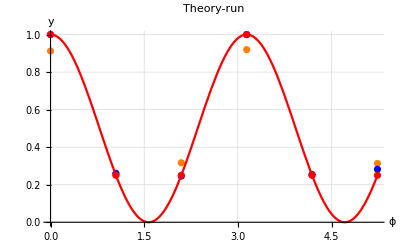

```mathematica
Show[Subscript[plot, run],Subscript[plot, sim],Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

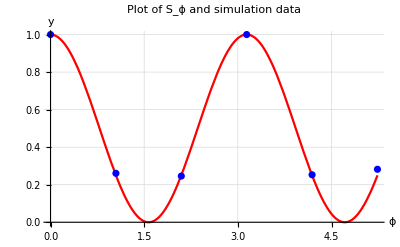

```mathematica
Subscript[S, sim]=Show[Subscript[plot, th],Subscript[plot, sim],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Plot of S_ϕ and simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

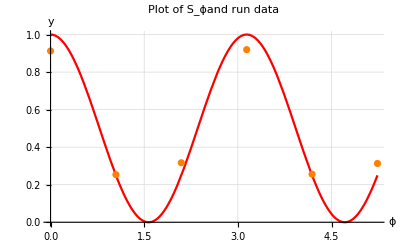

```mathematica
Subscript[S, run]=Show[Subscript[plot, th],Subscript[plot, run],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Plot of S_ϕand run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

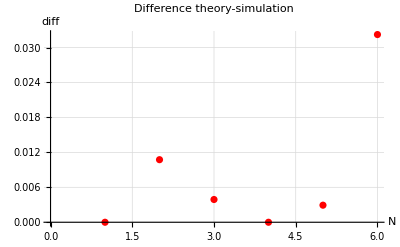

```mathematica
differenza=Abs[Subscript[list, th]-simulation];
ListPlot[differenza,AxesLabel->{HoldForm["N"],HoldForm["diff"]},PlotLabel->HoldForm["Difference theory-simulation"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

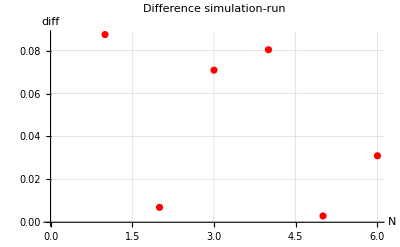

```mathematica
differenza=Abs[simulation-run];
ListPlot[differenza,AxesLabel->{HoldForm["N"],HoldForm["diff"]},PlotLabel->HoldForm["Difference simulation-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

Graphics to save

-Graphics-

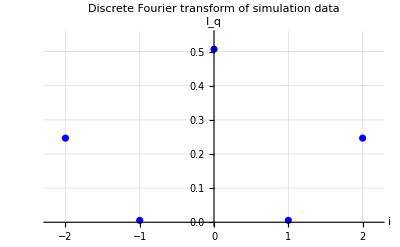

-Graphics-

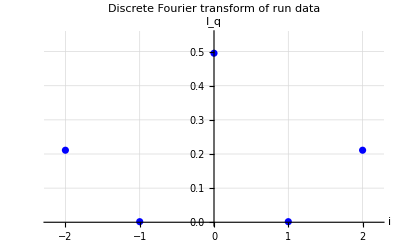

```mathematica
Subscript[S, sim]
Subscript[I, sim]
Subscript[S, run]
Subscript[I, run]
```

## N = 3

In this section the data refers to the measurement of qubit 0, with the parameter ϕ = (π j)/(n+1) that changes from 0 to (π (2n+1))/(n+1).

THEORY

```mathematica
n=3;
phi[j_]:=(Pi j)/(n+1)
S[ϕ_]:=1/2(1+Cos[n*ϕ])
Subscript[list, th]=Table[S[phi[j]],{j,0,(2*n+1)}];
```

```mathematica
Subscript[x, axis]=Table[phi[j],{j,0,(2*n+1)}];
```

```mathematica
Length[Subscript[x, axis]]==Length[Subscript[list, th]]
```

True

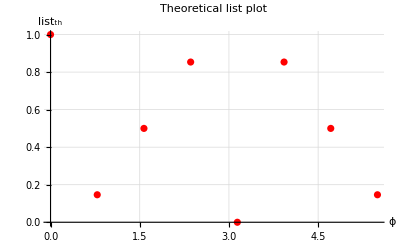

```mathematica
Subscript[listPlot, th]=ListPlot[Thread[{Subscript[x, axis],Subscript[list, th]}],AxesLabel->{HoldForm["ϕ"],HoldForm["list_th"]},PlotLabel->HoldForm["Theoretical list plot"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

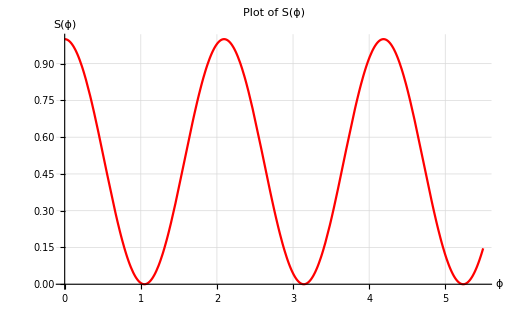

```mathematica
Subscript[plot, th]=Plot[S[ϕ],{ϕ,0,(Pi (2n+1))/(n+1)},AxesLabel->{HoldForm["ϕ"],HoldForm["S(ϕ)"]},PlotLabel->HoldForm["Plot of S(ϕ)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

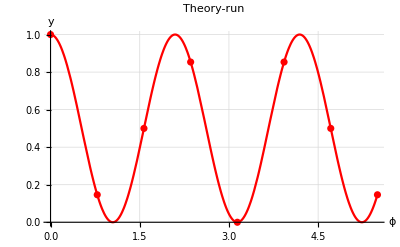

```mathematica
Show[Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, th]=Abs[N[Table[1/(2(n+1))*Sum[Exp[I  q phi[j]]*S[phi[j]],{j,0,(2*n+1)}],{q,-n,n}]]];
```

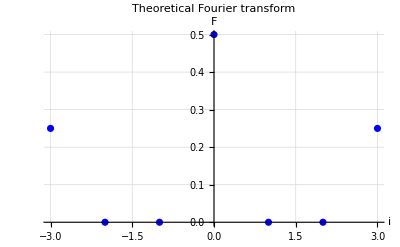

```mathematica
Subscript[FPlot, th]=ListPlot[Thread[{l,Subscript[F, th]}],AxesLabel->{HoldForm["i"],HoldForm["F"]},PlotLabel->HoldForm["Theoretical Fourier transform"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

SIMULATION

```mathematica
data1={1.0,0.1455078125,0.505859375,0.8623046875,0.0,0.8544921875,0.50390625,0.1396484375};
```

#### Plot of the data choosen

```mathematica
simulation= data1
Length[simulation]
```

{1.,0.145508,0.505859,0.862305,0.,0.854492,0.503906,0.139648}

8

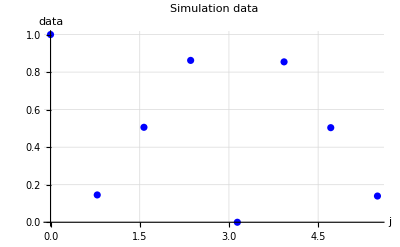

```mathematica
Subscript[plot, sim]=ListPlot[Thread[{Subscript[x, axis],simulation}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, sim]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*simulation[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

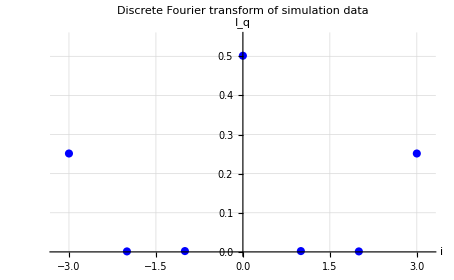

```mathematica
Subscript[I, sim]=Subscript[FPlot, sim]=ListPlot[Thread[{l,Subscript[F, sim]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{0,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

```mathematica
Lower=2 √(Subscript[F, sim][[Length[Subscript[F, sim]]]])
Upper=√(Subscript[F, sim][[n+1]]/2)+√(Subscript[F, sim][[Length[Subscript[F, sim]]]])
```

1.00308

1.00227

RUN

8192 shots

```mathematica
data1={0.26220703125,0.481201171875,0.5709228515625,0.2342529296875,0.1014404296875,0.3369140625,0.2923583984375,0.1524658203125};
data2={0.2847900390625,0.52099609375,0.5765380859375,0.24072265625,0.10546875,0.361328125,0.303466796875,0.158447265625};
data3 ={0.7325439453125,0.1209716796875,0.607177734375,0.615478515625,0.1146240234375,0.759521484375,0.3304443359375,0.2969970703125} ;
```

#### Plot of the data choosen

```mathematica
run=data2  (*inserire il data che si vuole*)
Length[run]
```

{0.28479,0.520996,0.576538,0.240723,0.105469,0.361328,0.303467,0.158447}

8

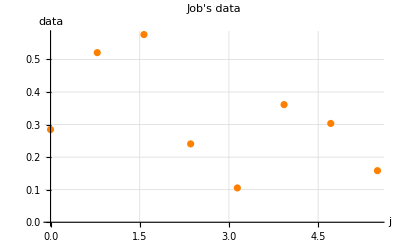

```mathematica
Subscript[plot, run]=ListPlot[Thread[{Subscript[x, axis],run}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Job's data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Orange}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, run]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*run[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

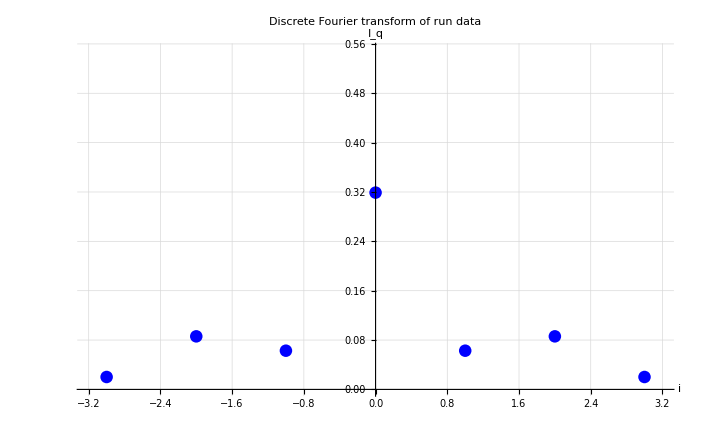

```mathematica
Subscript[I, run]=Subscript[FPlot, run]=ListPlot[Thread[{l,Subscript[F, run]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{0,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

Fidelity

```mathematica
F1=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data1[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}]
```

{0.0207967,0.082513,0.0604958,0.30397,0.0604958,0.082513,0.0207967}

```mathematica
F2=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data2[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

```mathematica
F3=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data3[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

```mathematica
F3Lower1= 2 √F1[[Length[F1]]]
F3Upper1=√(F1[[n+1]]/2)+√F1[[Length[F1]]]
```

0.288421

0.534063

```mathematica
F3Lower2= 2 √F2[[Length[F2]]]
F3Upper2=√(F2[[n+1]]/2)+√F2[[Length[F2]]]
```

0.28374

0.541226

```mathematica
F3Lower3= 2 √F3[[Length[F3]]]
F3Upper3=√(F3[[n+1]]/2)+√F3[[Length[F3]]]
```

0.83335

0.889549

COMPARE

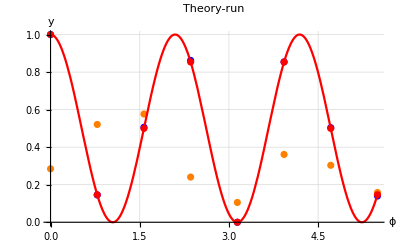

```mathematica
Show[Subscript[plot, run],Subscript[plot, sim],Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

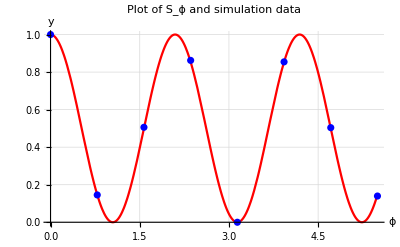

```mathematica
Subscript[S, sim]=Show[Subscript[plot, th],Subscript[plot, sim],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Plot of S_ϕ and simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

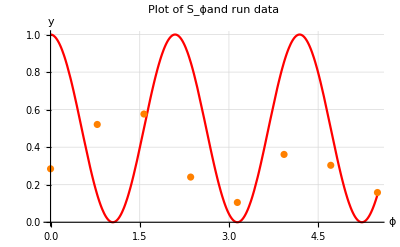

```mathematica
Subscript[S, run]=Show[Subscript[plot, th],Subscript[plot, run],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Plot of S_ϕand run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

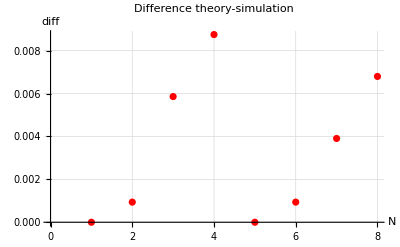

```mathematica
differenza=Abs[Subscript[list, th]-simulation];
ListPlot[differenza,AxesLabel->{HoldForm["N"],HoldForm["diff"]},PlotLabel->HoldForm["Difference theory-simulation"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

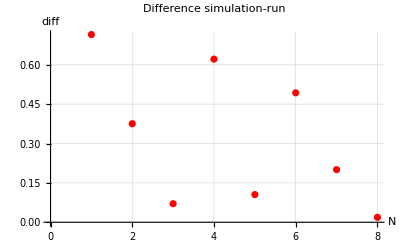

```mathematica
differenza=Abs[simulation-run];
ListPlot[differenza,AxesLabel->{HoldForm["N"],HoldForm["diff"]},PlotLabel->HoldForm["Difference simulation-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

Graphics to save

-Graphics-

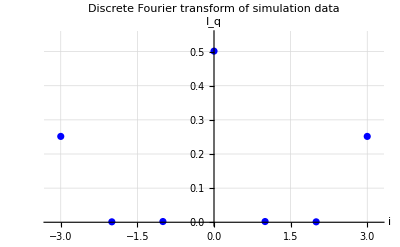

-Graphics-

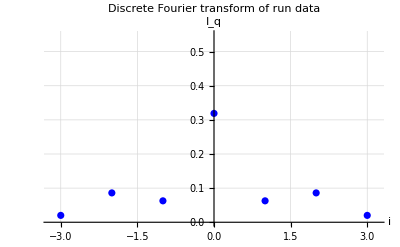

```mathematica
Subscript[S, sim]
Subscript[I, sim]
Subscript[S, run]
Subscript[I, run]
```

## N = 4

In this section the data refers to the measurement of qubit 0, with the parameter ϕ = (π j)/(n+1) that changes from 0 to (π (2n+1))/(n+1).

THEORY

```mathematica
n=4;
phi[j_]:=(Pi j)/(n+1)
S[ϕ_]:=1/2(1+Cos[n*ϕ])
Subscript[list, th]=Table[S[phi[j]],{j,0,(2*n+1)}];
```

```mathematica
Subscript[x, axis]=Table[phi[j],{j,0,(2*n+1)}];
```

```mathematica
Length[Subscript[x, axis]]==Length[Subscript[list, th]]
```

True

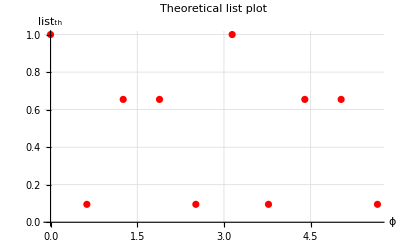

```mathematica
Subscript[listPlot, th]=ListPlot[Thread[{Subscript[x, axis],Subscript[list, th]}],AxesLabel->{HoldForm["ϕ"],HoldForm["list_th"]},PlotLabel->HoldForm["Theoretical list plot"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

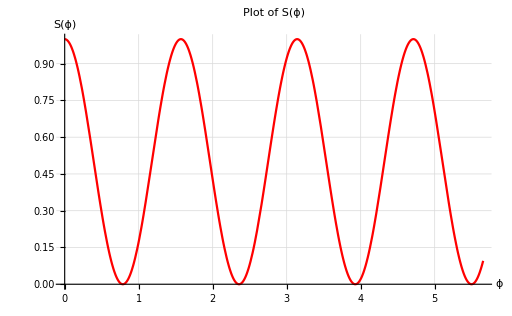

```mathematica
Subscript[plot, th]=Plot[S[ϕ],{ϕ,0,(Pi (2n+1))/(n+1)},AxesLabel->{HoldForm["ϕ"],HoldForm["S(ϕ)"]},PlotLabel->HoldForm["Plot of S(ϕ)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

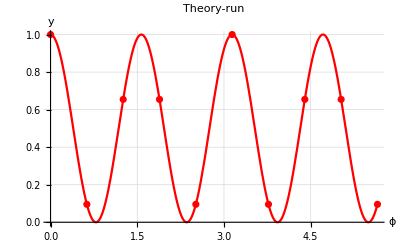

```mathematica
Show[Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, th]=Abs[N[Table[1/(2(n+1))*Sum[Exp[I  q phi[j]]*S[phi[j]],{j,0,(2*n+1)}],{q,-n,n}]]];
```

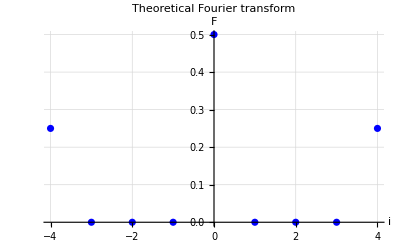

```mathematica
Subscript[FPlot, th]=ListPlot[Thread[{l,Subscript[F, th]}],AxesLabel->{HoldForm["i"],HoldForm["F"]},PlotLabel->HoldForm["Theoretical Fourier transform"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

SIMULATION

```mathematica
data1={1.0,0.0791015625,0.640625,0.6064453125,0.0986328125,1.0,0.0927734375,0.6787109375,0.6376953125,0.1044921875};
```

#### Plot of the data choosen

```mathematica
simulation= data1
Length[simulation]
```

{1.,0.0791016,0.640625,0.606445,0.0986328,1.,0.0927734,0.678711,0.637695,0.104492}

10

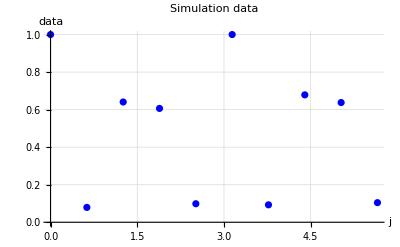

```mathematica
Subscript[plot, sim]=ListPlot[Thread[{Subscript[x, axis],simulation}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, sim]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*simulation[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

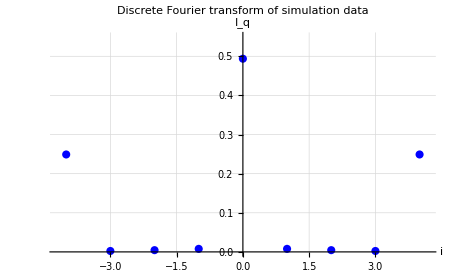

```mathematica
Subscript[I, sim]=Subscript[FPlot, sim]=ListPlot[Thread[{l,Subscript[F, sim]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{0,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

```mathematica
Lower=2 √(Subscript[F, sim][[Length[Subscript[F, sim]]]])
Upper=√(Subscript[F, sim][[n+1]]/2)+√(Subscript[F, sim][[Length[Subscript[F, sim]]]])
```

0.998078

0.995953

RUN

8192 shots

```mathematica
data1={0.25244140625,0.4315185546875,0.5384521484375,0.295654296875,0.148193359375,0.23876953125,0.4075927734375,0.4971923828125,0.266845703125,0.1510009765625};
data2={0.251220703125,0.44482421875,0.5362548828125,0.2967529296875,0.1500244140625,0.2293701171875,0.4195556640625,0.4984130859375,0.2760009765625,0.149658203125};
data3 = {0.5123291015625,0.135009765625,0.6019287109375,0.3050537109375,0.2872314453125,0.5235595703125,0.1396484375,0.5631103515625,0.2840576171875,0.3095703125};
```

#### Plot of the data choosen

```mathematica
run=data3  (*inserire il data che si vuole*)
Length[run]
```

{0.512329,0.13501,0.601929,0.305054,0.287231,0.52356,0.139648,0.56311,0.284058,0.30957}

10

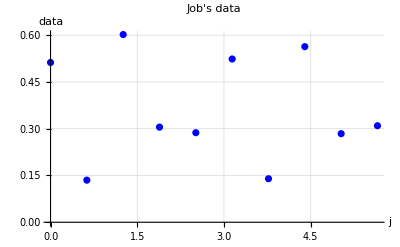

```mathematica
Subscript[plot, run]=ListPlot[Thread[{Subscript[x, axis],run}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Job's data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, run]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*run[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

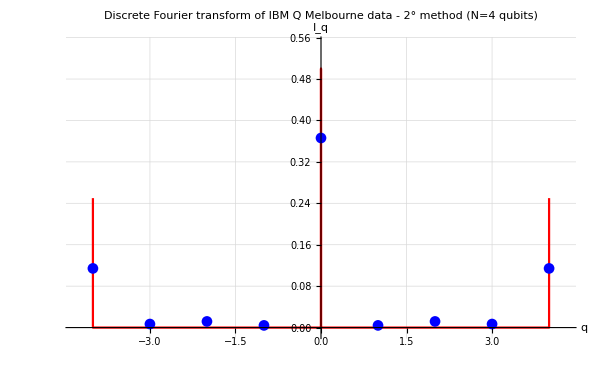

```mathematica
Subscript[I, run]=Subscript[FPlot, run]=ListPlot[Thread[{l,Subscript[F, run]}],AxesLabel->{Style["i",Black,FontFamily->"HoldForm",FontSize->16],Style["I_q",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Discrete Fourier transform of 'ibmq melbourne' run 2° method data (N=4 qubit)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{0,0.55}}, PlotLegends->{},PlotStyle->{Blue}];
verticalSize=430;
orSize=600;
Fideale=Insert[Insert[Insert[Insert[Subscript[F, th],0,2],0,n+1+1],0,n+1+1+1+1],0,2n+1+1+1+1];
lideale=Insert[Insert[Insert[Insert[l,-n,2],0,n+1+1],0,n+1+1+1+1],n,2n+1+1+1+1];
FPlotideale=ListLinePlot[Thread[{lideale,Fideale}],AxesLabel->{Style["q",Black,FontFamily->"HoldForm",FontSize->16],Style["I_q",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Discrete Fourier transform of ideal simulation data (N=6 qubits)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{-0.01,0.55}}, PlotLegends->{},PlotStyle->{Red}];

Show[FPlotideale,Subscript[FPlot, run],AxesLabel->{Style["q",Black,FontFamily->"HoldForm",FontSize->20],Style["I_q",Black,FontFamily->"HoldForm",FontSize->20]},PlotLabel->HoldForm["Discrete Fourier transform of IBM Q Melbourne data - 2° method (N=4 qubits)"],LabelStyle->{FontFamily->"Calibri",13,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Directive[18], GridLines->Automatic , PlotRange->{{-n-0.3,n+0.3},{-0.01,0.55}}, PlotLegends->{},PlotStyle->{Red} ,ImageSize->{orSize,verticalSize}]
```

Fidelity

```mathematica
F1=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data1[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}]
```

{0.0147334,0.00216095,0.0910545,0.0088214,0.322766,0.0088214,0.0910545,0.00216095,0.0147334}

```mathematica
F2=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data2[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

```mathematica
F3=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data3[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

```mathematica
F4Lower1= 2 √F1[[Length[F1]]]
F4Upper1=√(F1[[n+1]]/2)+√F1[[Length[F1]]]
```

0.242762

0.523106

```mathematica
F4Lower2= 2 √F2[[Length[F2]]]
F4Upper2=√(F2[[n+1]]/2)+√F2[[Length[F2]]]
```

0.212718

0.5096

```mathematica
F4Lower3= 2 √F3[[Length[F3]]]
F4Upper3=√(F3[[n+1]]/2)+√F3[[Length[F3]]]
```

0.676017

0.765881

COMPARE

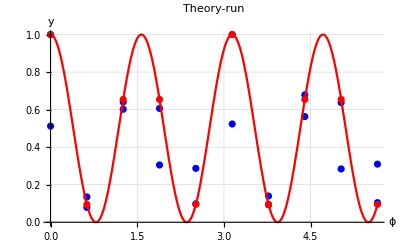

```mathematica
Show[Subscript[plot, run],Subscript[plot, sim],Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

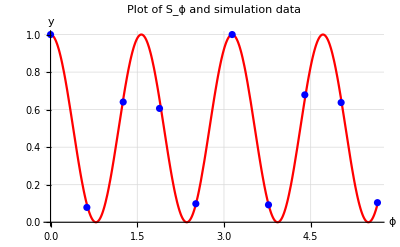

```mathematica
Subscript[S, sim]=Show[Subscript[plot, th],Subscript[plot, sim],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Plot of S_ϕ and simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

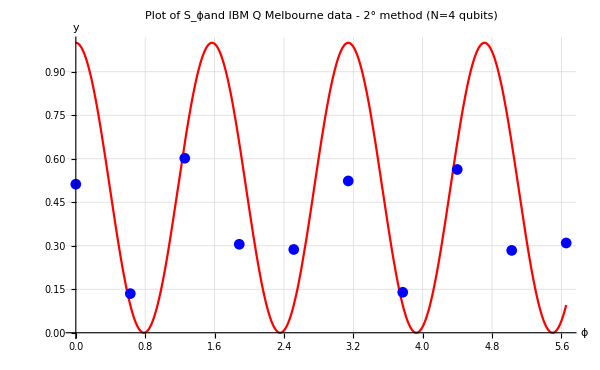

```mathematica
Subscript[S, run]=Show[Subscript[plot, th],Subscript[plot, run],AxesLabel->{Style["ϕ",Black,FontFamily->"HoldForm",FontSize->20],Style["y",Black,FontFamily->"HoldForm",FontSize->20]},PlotLabel->HoldForm["Plot of S_ϕand IBM Q Melbourne data - 2° method (N=4 qubits)"],LabelStyle->{FontFamily->"Calibri",16,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Directive[18], GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},ImageSize->{orSize,verticalSize}]
```

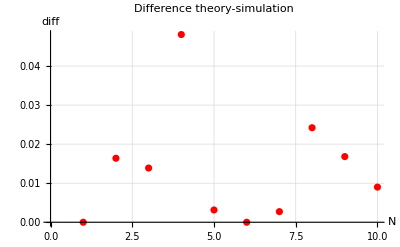

```mathematica
differenza=Abs[Subscript[list, th]-simulation];
ListPlot[differenza,AxesLabel->{HoldForm["N"],HoldForm["diff"]},PlotLabel->HoldForm["Difference theory-simulation"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

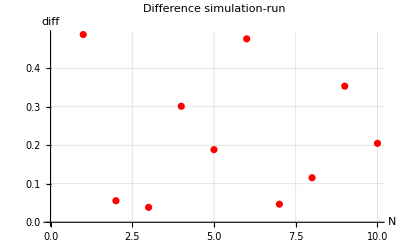

```mathematica
differenza=Abs[simulation-run];
ListPlot[differenza,AxesLabel->{HoldForm["N"],HoldForm["diff"]},PlotLabel->HoldForm["Difference simulation-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

Graphics to save

-Graphics-

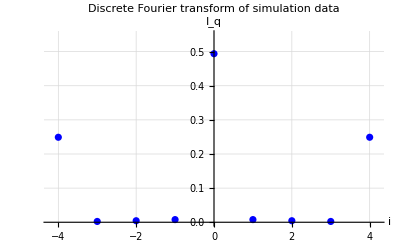

-Graphics-

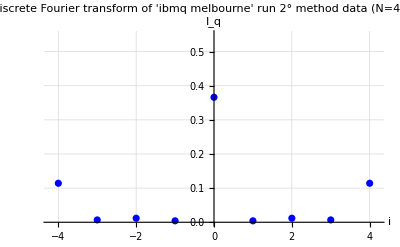

```mathematica
Subscript[S, sim]
Subscript[I, sim]
Subscript[S, run]
Subscript[I, run]
```

## N = 5

In this section the data refers to the measurement of qubit 0, with the parameter ϕ = (π j)/(n+1) that changes from 0 to (π (2n+1))/(n+1).

THEORY

```mathematica
n=5;
phi[j_]:=(Pi j)/(n+1)
S[ϕ_]:=1/2(1+Cos[n*ϕ])
Subscript[list, th]=Table[S[phi[j]],{j,0,(2*n+1)}];
```

```mathematica
Subscript[x, axis]=Table[phi[j],{j,0,(2*n+1)}];
```

```mathematica
Length[Subscript[x, axis]]==Length[Subscript[list, th]]
```

True

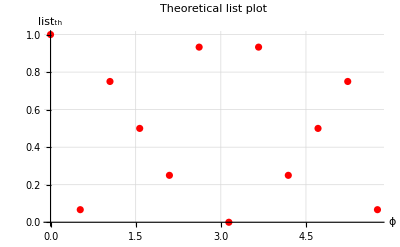

```mathematica
Subscript[listPlot, th]=ListPlot[Thread[{Subscript[x, axis],Subscript[list, th]}],AxesLabel->{HoldForm["ϕ"],HoldForm["list_th"]},PlotLabel->HoldForm["Theoretical list plot"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

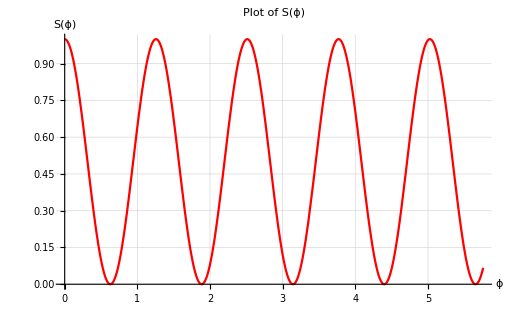

```mathematica
Subscript[plot, th]=Plot[S[ϕ],{ϕ,0,(Pi (2n+1))/(n+1)},AxesLabel->{HoldForm["ϕ"],HoldForm["S(ϕ)"]},PlotLabel->HoldForm["Plot of S(ϕ)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

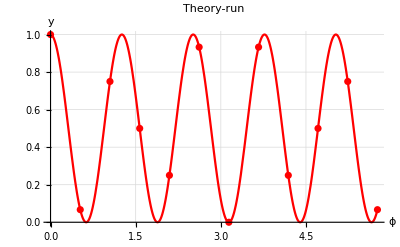

```mathematica
Show[Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, th]=Abs[N[Table[1/(2(n+1))*Sum[Exp[I  q phi[j]]*S[phi[j]],{j,0,(2*n+1)}],{q,-n,n}]]];
```

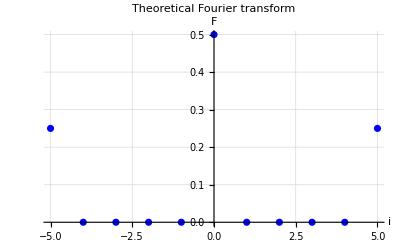

```mathematica
Subscript[FPlot, th]=ListPlot[Thread[{l,Subscript[F, th]}],AxesLabel->{HoldForm["i"],HoldForm["F"]},PlotLabel->HoldForm["Theoretical Fourier transform"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

SIMULATION

```mathematica
data1={1.0,0.0751953125,0.7353515625,0.5009765625,0.2568359375,0.943359375,0.0,0.9306640625,0.2421875,0.494140625,0.728515625,0.0595703125};
```

#### Plot of the data choosen

```mathematica
simulation= data1
Length[simulation]
```

{1.,0.0751953,0.735352,0.500977,0.256836,0.943359,0.,0.930664,0.242188,0.494141,0.728516,0.0595703}

12

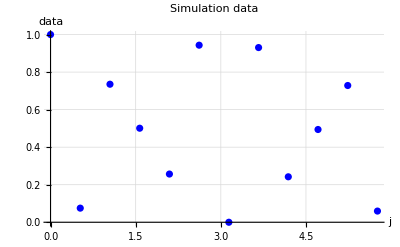

```mathematica
Subscript[plot, sim]=ListPlot[Thread[{Subscript[x, axis],simulation}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, sim]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*simulation[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

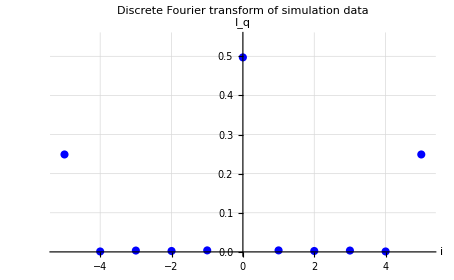

```mathematica
Subscript[I, sim]=Subscript[FPlot, sim]=ListPlot[Thread[{l,Subscript[F, sim]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{0,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

```mathematica
Lower=2 √(Subscript[F, sim][[Length[Subscript[F, sim]]]])
Upper=√(Subscript[F, sim][[n+1]]/2)+√(Subscript[F, sim][[Length[Subscript[F, sim]]]])
```

0.998109

0.997669

RUN

8192 shots

```mathematica
data1={0.1337890625,0.149658203125,0.101806640625,0.064208984375,0.06005859375,0.0926513671875,0.13037109375,0.1162109375,0.08203125,0.057373046875,0.05859375,0.09716796875};
data2={0.1309814453125,0.1446533203125,0.097900390625,0.058349609375,0.061279296875,0.0927734375,0.122314453125,0.1192626953125,0.0850830078125,0.055908203125,0.0638427734375,0.0948486328125};
data3 = {0.1324462890625,0.2469482421875,0.142822265625,0.190673828125,0.176025390625,0.181640625,0.277099609375,0.12744140625,0.21240234375,0.1744384765625,0.1749267578125,0.1922607421875};
```

#### Plot of the data choosen

```mathematica
run=data3  (*inserire il data che si vuole*)
Length[run]
```

{0.132446,0.246948,0.142822,0.190674,0.176025,0.181641,0.2771,0.127441,0.212402,0.174438,0.174927,0.192261}

12

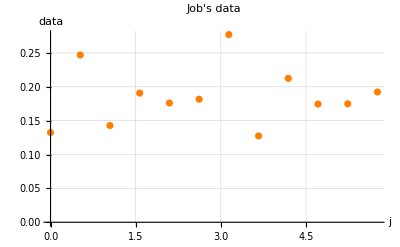

```mathematica
Subscript[plot, run]=ListPlot[Thread[{Subscript[x, axis],run}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Job's data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Orange}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, run]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*run[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

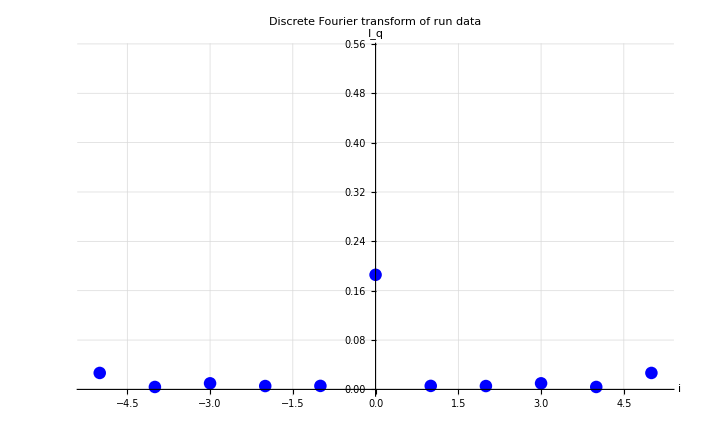

```mathematica
Subscript[I, run]=Subscript[FPlot, run]=ListPlot[Thread[{l,Subscript[F, run]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{0,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

Fidelity

```mathematica
F1=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data1[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}]
```

{0.00170929,0.000960267,0.00222043,0.0209164,0.00502877,0.0953267,0.00502877,0.0209164,0.00222043,0.000960267,0.00170929}

```mathematica
F2=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data2[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

```mathematica
F3=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data3[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

```mathematica
F5Lower1= 2 √F1[[Length[F1]]]
F5Upper1=√(F1[[n+1]]/2)+√F1[[Length[F1]]]
```

0.082687

0.259663

```mathematica
F5Lower2= 2 √F2[[Length[F2]]]
F5Upper2=√(F2[[n+1]]/2)+√F2[[Length[F2]]]
```

0.0550112

0.244223

```mathematica
F5Lower3= 2 √F3[[Length[F3]]]
F5Upper3=√(F3[[n+1]]/2)+√F3[[Length[F3]]]
```

0.326727

0.468126

COMPARE

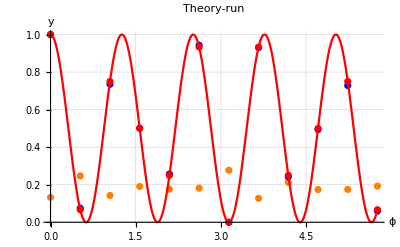

```mathematica
Show[Subscript[plot, run],Subscript[plot, sim],Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

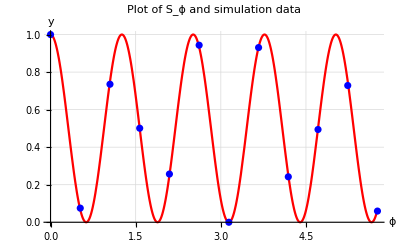

```mathematica
Subscript[S, sim]=Show[Subscript[plot, th],Subscript[plot, sim],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Plot of S_ϕ and simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

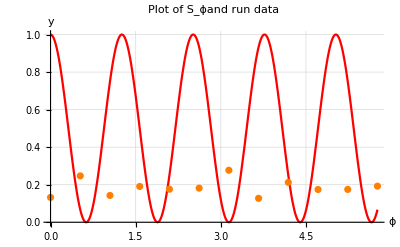

```mathematica
Subscript[S, run]=Show[Subscript[plot, th],Subscript[plot, run],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Plot of S_ϕand run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

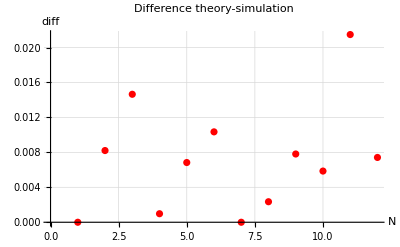

```mathematica
differenza=Abs[Subscript[list, th]-simulation];
ListPlot[differenza,AxesLabel->{HoldForm["N"],HoldForm["diff"]},PlotLabel->HoldForm["Difference theory-simulation"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

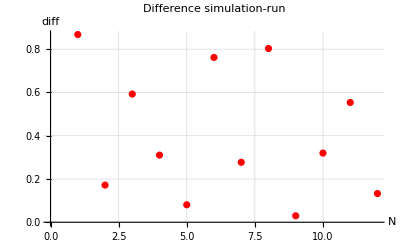

```mathematica
differenza=Abs[simulation-run];
ListPlot[differenza,AxesLabel->{HoldForm["N"],HoldForm["diff"]},PlotLabel->HoldForm["Difference simulation-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

Graphics to save

-Graphics-

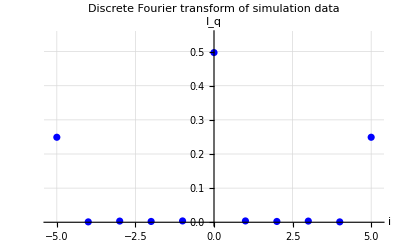

-Graphics-

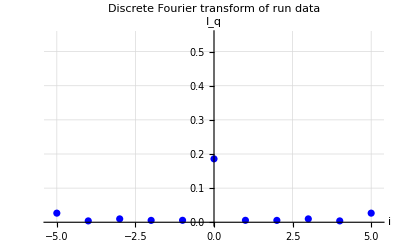

```mathematica
Subscript[S, sim]
Subscript[I, sim]
Subscript[S, run]
Subscript[I, run]
```

## N = 6

In this section the data refers to the measurement of qubit 0, with the parameter ϕ = (π j)/(n+1) that changes from 0 to (π (2n+1))/(n+1).

THEORY

```mathematica
n=6;
phi[j_]:=(Pi j)/(n+1)
S[ϕ_]:=1/2(1+Cos[n*ϕ])
Subscript[list, th]=Table[S[phi[j]],{j,0,(2*n+1)}];
```

```mathematica
Subscript[x, axis]=Table[phi[j],{j,0,(2*n+1)}];
```

```mathematica
Length[Subscript[x, axis]]==Length[Subscript[list, th]]
```

True

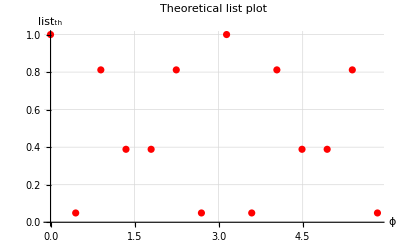

```mathematica
Subscript[listPlot, th]=ListPlot[Thread[{Subscript[x, axis],Subscript[list, th]}],AxesLabel->{HoldForm["ϕ"],HoldForm["list_th"]},PlotLabel->HoldForm["Theoretical list plot"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

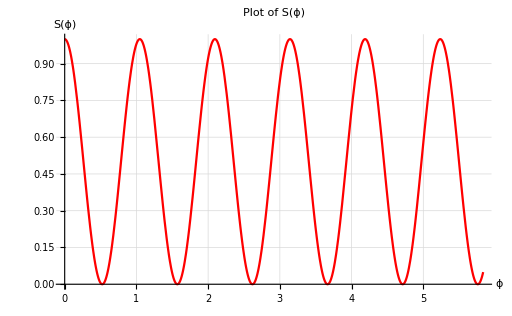

```mathematica
Subscript[plot, th]=Plot[S[ϕ],{ϕ,0,(Pi (2n+1))/(n+1)},AxesLabel->{HoldForm["ϕ"],HoldForm["S(ϕ)"]},PlotLabel->HoldForm["Plot of S(ϕ)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

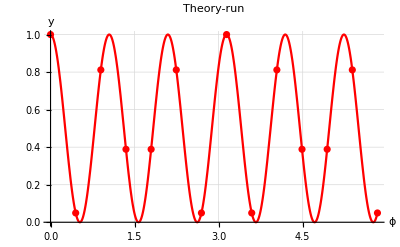

```mathematica
Show[Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, th]=Abs[N[Table[1/(2(n+1))*Sum[Exp[I  q phi[j]]*S[phi[j]],{j,0,(2*n+1)}],{q,-n,n}]]];
```

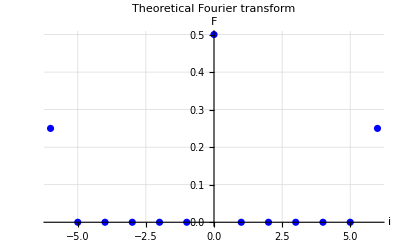

```mathematica
Subscript[FPlot, th]=ListPlot[Thread[{l,Subscript[F, th]}],AxesLabel->{HoldForm["i"],HoldForm["F"]},PlotLabel->HoldForm["Theoretical Fourier transform"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

SIMULATION

```mathematica
data1={1.0,0.04296875,0.8056640625,0.400390625,0.3798828125,0.80859375,0.0498046875,1.0,0.0556640625,0.8173828125,0.39453125,0.396484375,0.8203125,0.0517578125};
```

#### Plot of the data choosen

```mathematica
simulation= data1
Length[simulation]
```

{1.,0.0429688,0.805664,0.400391,0.379883,0.808594,0.0498047,1.,0.0556641,0.817383,0.394531,0.396484,0.820313,0.0517578}

14

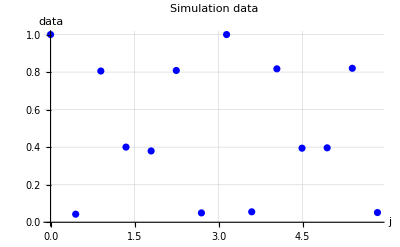

```mathematica
Subscript[plot, sim]=ListPlot[Thread[{Subscript[x, axis],simulation}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, sim]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*simulation[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

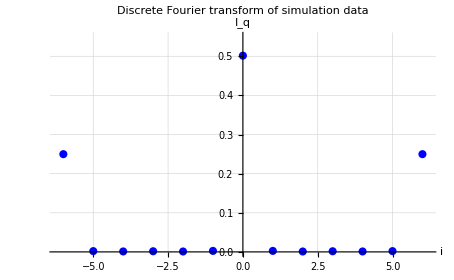

```mathematica
Subscript[I, sim]=Subscript[FPlot, sim]=ListPlot[Thread[{l,Subscript[F, sim]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{0,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

```mathematica
Lower=2 √(Subscript[F, sim][[Length[Subscript[F, sim]]]])
Upper=√(Subscript[F, sim][[n+1]]/2)+√(Subscript[F, sim][[Length[Subscript[F, sim]]]])
```

0.999659

1.00067

RUN

8192 shots

```mathematica
data1={0.0589599609375,0.054931640625,0.0390625,0.035888671875,0.03955078125,0.057373046875,0.08251953125,0.080078125,0.0675048828125,0.0487060546875,0.0369873046875,0.0413818359375,0.0447998046875,0.0523681640625};
data2={0.05322265625,0.0516357421875,0.048828125,0.0440673828125,0.0535888671875,0.06298828125,0.07373046875,0.07470703125,0.0645751953125,0.0546875,0.042236328125,0.0457763671875,0.0477294921875,0.053955078125};
data3 ={0.0791015625,0.0694580078125,0.0537109375,0.0562744140625,0.0572509765625,0.04541015625,0.046630859375,0.0478515625,0.04345703125,0.044921875,0.0589599609375,0.072998046875,0.0836181640625,0.0657958984375};
```

#### Plot of the data choosen

```mathematica
run=data2  (*inserire il data che si vuole*)
Length[run]
```

{0.0532227,0.0516357,0.0488281,0.0440674,0.0535889,0.0629883,0.0737305,0.074707,0.0645752,0.0546875,0.0422363,0.0457764,0.0477295,0.0539551}

14

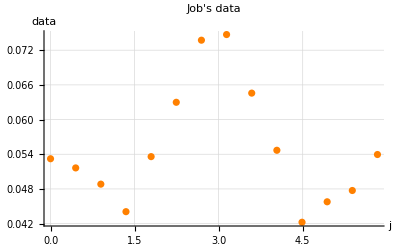

```mathematica
Subscript[plot, run]=ListPlot[Thread[{Subscript[x, axis],run}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Job's data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Orange}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, run]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*run[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

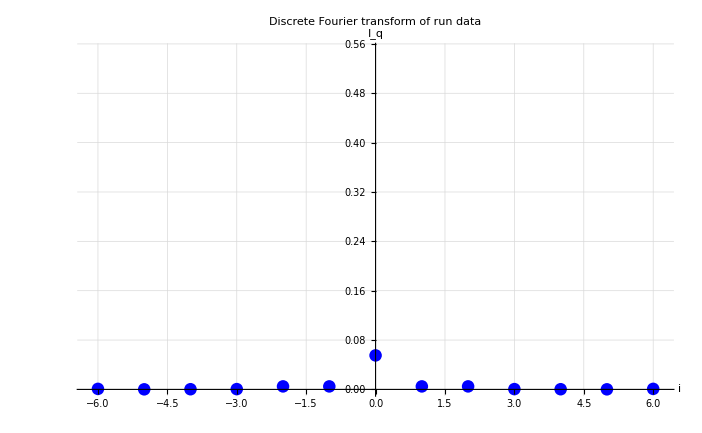

```mathematica
Subscript[I, run]=Subscript[FPlot, run]=ListPlot[Thread[{l,Subscript[F, run]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{0,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

Fidelity

```mathematica
F1=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data1[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}]
```

{0.00063075,0.00105027,0.000468405,0.00167651,0.00869493,0.00526,0.0528652,0.00526,0.00869493,0.00167651,0.000468405,0.00105027,0.00063075}

```mathematica
F2=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data2[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

```mathematica
F3=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data3[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

```mathematica
F6Lower1= 2 √F1[[Length[F1]]]
F6Upper1=√(F1[[n+1]]/2)+√F1[[Length[F1]]]
```

0.0502295

0.187696

```mathematica
F6Lower2= 2 √F2[[Length[F2]]]
F6Upper2=√(F2[[n+1]]/2)+√F2[[Length[F2]]]
```

0.0587731

0.195404

```mathematica
F6Lower3= 2 √F3[[Length[F3]]]
F6Upper3=√(F3[[n+1]]/2)+√F3[[Length[F3]]]
```

0.0646256

0.20401

COMPARE

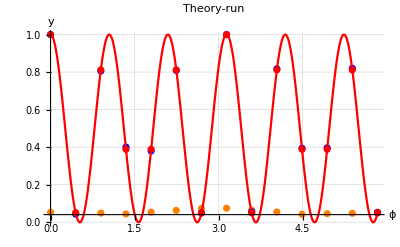

```mathematica
Show[Subscript[plot, run],Subscript[plot, sim],Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

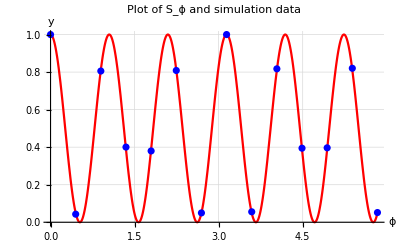

```mathematica
Subscript[S, sim]=Show[Subscript[plot, th],Subscript[plot, sim],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Plot of S_ϕ and simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

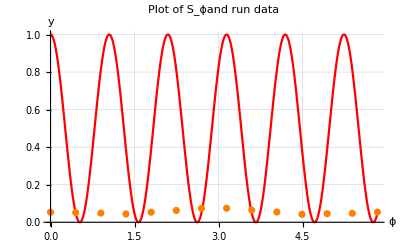

```mathematica
Subscript[S, run]=Show[Subscript[plot, th],Subscript[plot, run],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Plot of S_ϕand run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

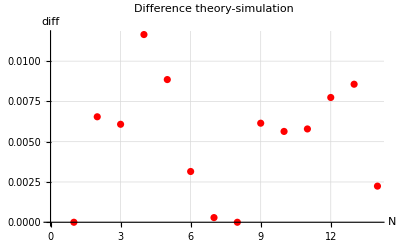

```mathematica
differenza=Abs[Subscript[list, th]-simulation];
ListPlot[differenza,AxesLabel->{HoldForm["N"],HoldForm["diff"]},PlotLabel->HoldForm["Difference theory-simulation"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

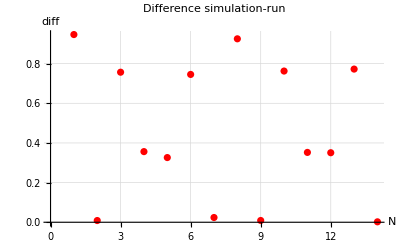

```mathematica
differenza=Abs[simulation-run];
ListPlot[differenza,AxesLabel->{HoldForm["N"],HoldForm["diff"]},PlotLabel->HoldForm["Difference simulation-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

Graphics to save

-Graphics-

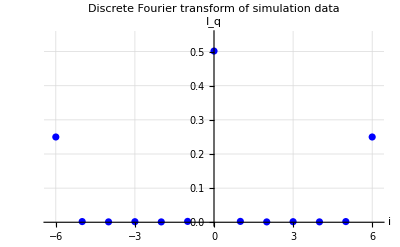

-Graphics-

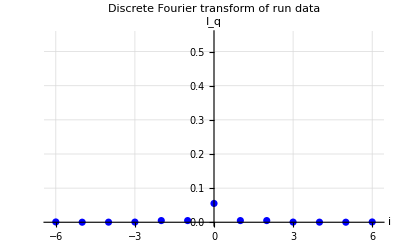

```mathematica
Subscript[S, sim]
Subscript[I, sim]
Subscript[S, run]
Subscript[I, run]
```

## Fidelity plot

No transpile:

```mathematica
VLower1={F2Lower1,F3Lower1,F4Lower1,F5Lower1,F6Lower1}
VUpper1={F2Upper1,F3Upper1,F4Upper1,F5Upper1,F6Upper1};
```

{0.9023,0.288421,0.242762,0.082687,0.0502295}

Transpile:

```mathematica
VLower2={F2Lower2,F3Lower2,F4Lower2,F5Lower2,F6Lower2};
VUpper2={F2Upper2,F3Upper2,F4Upper2,F5Upper2,F6Upper2};
```

Transpile user:

```mathematica
VLower3={F2Lower3,F3Lower3,F4Lower3,F5Lower3,F6Lower3};
VUpper3={F2Upper3,F3Upper3,F4Upper3,F5Upper3,F6Upper3};
```

```mathematica
qubits={2,3,4,5,6}
```

{2,3,4,5,6}

```mathematica
Thread[{qubits,VLower1}]
```

{{2,0.9023},{3,0.288421},{4,0.242762},{5,0.082687},{6,0.0502295}}

```mathematica
retta=Plot[0.5,{x,0,6.5},PlotStyle->{Dashing[Tiny],Dashing[Large],Black}];
```

```mathematica
P1L=ListPlot[Thread[{qubits,VLower1}],AxesLabel->{HoldForm["N"],HoldForm["Fidelity"]},PlotLabel->HoldForm["Fidelity bound"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{1.5,6.5},{0,1}}, PlotLegends->{},PlotStyle->{Green}];
P1U=ListPlot[Thread[{qubits,VUpper1}],AxesLabel->{HoldForm["N"],HoldForm["Fidelity"]},PlotLabel->HoldForm["Fidelity bound"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic ,  PlotRange->{{1.5,6.5},{0,1}}, PlotLegends->{},PlotStyle->{Orange}];

P2L=ListPlot[Thread[{qubits,VLower2}],AxesLabel->{HoldForm["N"],HoldForm["Fidelity"]},PlotLabel->HoldForm["Fidelity bound"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{1.5,6.5},{0,1}}, PlotLegends->{},PlotStyle->{Green}];
P2U=ListPlot[Thread[{qubits,VUpper2}],AxesLabel->{HoldForm["N"],HoldForm["Fidelity"]},PlotLabel->HoldForm["Fidelity bound"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic ,  PlotRange->{{1.5,6.5},{0,1}}, PlotLegends->{},PlotStyle->{Orange}];

P3L=ListPlot[Thread[{qubits,VLower3}],AxesLabel->{HoldForm["N"],HoldForm["Fidelity"]},PlotLabel->HoldForm["Fidelity bound"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{1.5,6.5},{0,1}}, PlotLegends->{},PlotStyle->{Green}];
P3U=ListPlot[Thread[{qubits,VUpper3}],AxesLabel->{HoldForm["N"],HoldForm["Fidelity"]},PlotLabel->HoldForm["Fidelity bound"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic ,  PlotRange->{{1.5,6.5},{0,1}}, PlotLegends->{},PlotStyle->{Orange}];
```

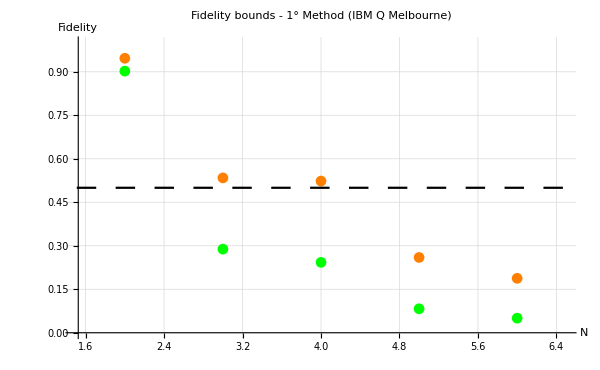

```mathematica
a=Show[P1L,P1U,retta,AxesLabel->{Style["N",Black,FontFamily->"HoldForm",FontSize->16],Style["Fidelity",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Fidelity bounds - 1° Method (IBM Q Melbourne)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic ,  PlotRange->{{1.5,6.5},{0,1}}, PlotLegends->{},PlotStyle->{Red},ImageSize->{orSize,verticalSize}]
```

```mathematica
r=Show[P2L,P2U,retta];
```

```mathematica
salvare=ListPlot[{Thread[{qubits,VLower3}],Thread[{qubits,VUpper3}]},Filling->{1->{2}},FillingStyle->{Black},PlotStyle->{RGBColor[0.17,0.66,0.08],Orange},AxesLabel->{Style["N",Black,FontFamily->"HoldForm",FontSize->20],Style["Fidelity",Black,FontFamily->"HoldForm",FontSize->20]},PlotLabel->HoldForm["Fidelity bounds - 2° Method (IBM Q Melbourne)"],LabelStyle->{FontFamily->"Calibri",20,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Directive[18], GridLines->Automatic ,  PlotRange->{{1.5,6.5},{0,1}}, PlotLegends->{},ImageSize->{orSize,verticalSize}];
```

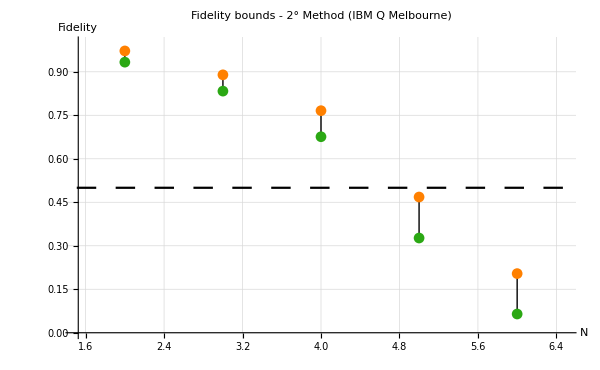

```mathematica
Show[salvare,retta]
```

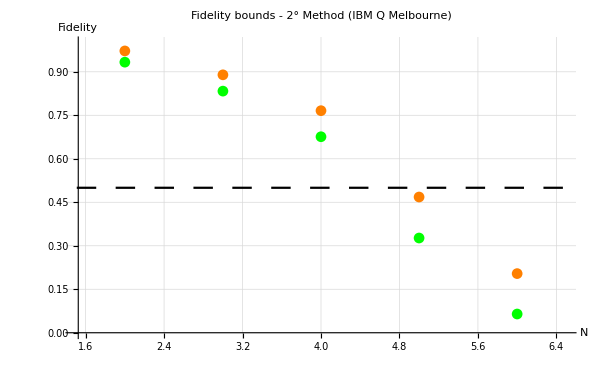

```mathematica
m=Show[P3L,P3U,retta, AxesLabel->{Style["N",Black,FontFamily->"HoldForm",FontSize->16],Style["Fidelity",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Fidelity bounds - 2° Method (IBM Q Melbourne)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic ,  PlotRange->{{1.5,6.5},{0,1}}, PlotLegends->{},PlotStyle->{Red},ImageSize->{orSize,verticalSize}]
```

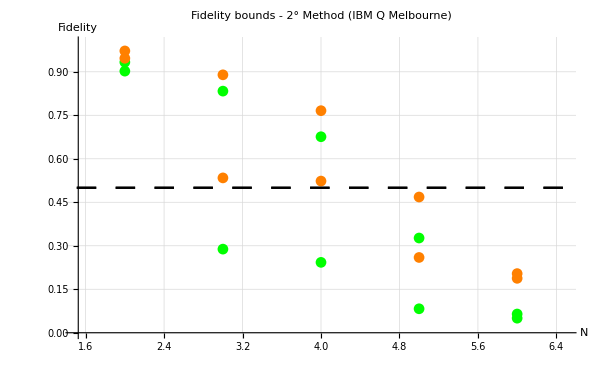

```mathematica
Show[m,a]
```